# Homework 16

## Problem 16.1

Write down the Lagrangian for a simple pendulum as a function of θ (theta) and dθ/dt.
	m is the mass of the pendulum (the rod is massless).
	d is the length of the pendulum.
	theta is the pendulum angle. It is 0 when the pendulum is straight down.
	thetadot is dθ / dt.
Find the equation of motion for the system.
Find the equation of motion for the small angle approximation.
Determine the motion of the pendulum for initial conditions theta=π/6 and theta = π–0.1, with d = 0.2482 m and m = 0.5 kg.

## Part A

Write down the Lagrangian.  Use thetadot for this part of the homework; not  theta'.  If you use theta', then Mathematica may try to make some calculations that you don't want it to do right now.

```mathematica
Quit[]
```

```mathematica
L=1/2*m*d^2*thetadot^2-m*g*d(1-Cos[theta])
```

1/2 d^2 m thetadot^2-d g m (1-Cos[theta])

### Solution

```mathematica
d1=D[L,theta];
d2=D[L,thetadot];
If[d2==0,Print["You need to write L explicitly as a function of thetadot and theta."]];
If[d1==0,Print["You need to write L explicitly as a function of thetadot and theta."]];
OK=1;
If[FullSimplify[Solve[d1==-m*g*d*Sin[theta],m]]≠{{}},OK=0];
If[FullSimplify[Solve[d2==m*d^2*thetadot,m]]≠{{}},OK=0];
If[OK==1,Print["L is correct"],Print["L is incorrect"]];
If[FullSimplify[Solve[d1==m*g*d*Sin[theta],m]]=={{}},Print["Your potential energy has the wrong sign"]];
```

L is correct

## Part B

Find the derivatives of the Lagrangian with respect to theta and thetadot. 
As you do this, replace theta with theta[t] and thetadot with theta’ [t] using the code provided.

```mathematica
dLdtheta=D[L,theta]/.{theta->theta[t],thetadot->theta'[t]}
dLdthetadot=D[L,thetadot]/.{theta->theta[t],thetadot->theta'[t]}
```

-d g m Sin[theta[t]]

d^2 m theta'[t]

```mathematica
eq1=dLdtheta==D[dLdthetadot,t]
```

-d g m Sin[theta[t]]==d^2 m theta''[t]

### Solution

The correct expression is -d g m Sin[theta[t]]==d^2 m theta''[t]

## Part C

Now make the small angle approximation for this equation.

### What is the small angle approximation?

The small angle approximation means that we replace trig functions by the smallest number of terms in their Taylor series expansion that give a non-trivial solution.
Generally, Sin[ θ ] is replaced by θ and Cos[ θ ] by 1 (sometimes Cos[θ]=1 - 1/2 θ^2, but not in this case).

```mathematica
eq2=-d g m *theta[t]==d^2 m theta''[t]
```

-d g m theta[t]==d^2 m theta''[t]

### Solution

The correct expression is -d g m theta[t]==d^2 m theta''[t]

## Part D

Now we enter numerical values and plot the results.

First, we choose a relatively small starting angle. How well do the full equation and the small - angle approximation agree?

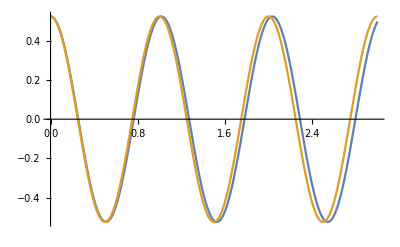

```mathematica
d=.2482;
g=9.8;
m=.5;
bc={theta[0]==Pi/6,theta'[0]==0};
sol1=NDSolve[{eq1,bc},theta[t],{t,0,3}];
sol2=NDSolve[{eq2,bc},theta[t],{t,0,3}];
Plot[{theta[t]/.sol1,theta[t]/.sol2},{t,0,3}]
```

Next, we choose a much larger starting angle. Do the results still agree well?

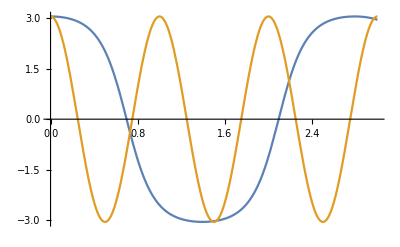

```mathematica
bc1={theta[0]==Pi-.1,theta'[0]==0};
sol3=NDSolve[{eq1,bc1},theta[t],{t,0,3}];
sol4=NDSolve[{eq2,bc1},theta[t],{t,0,3}];
Plot[{theta[t]/.sol3,theta[t]/.sol4},{t,0,3}]
```

The results do not agree.

For very large angles, the small angle approximation is not close at all. The general solution to the pendulum problem can be written in terms of "elliptic integrals."

## Problem 16.2

A mass m moves in a three-dimensional, nonlinear oscillator of potential U=1/2*k r^2+1/4*s r^4. It is also subject to gravity.
Work in Cartesian coordinates and let the upward direction be z. 
The values of the constants are k=0.3, s=100 in SI units.
The initial conditions are:  x(0)=0.0005 m, vx(0)=0, y(0)=0, vy(0)=0.1 m/s, z(0)=0, vz(0)=-0.3 m/s.

```mathematica
Quit[]
```

A) Write down T and U in Cartesian coordinates x, y, and z, together with xdot, ydot, and zdot.  Find the Lagrangian.

```mathematica
T=1/2*m*(xdot^2+ydot^2+zdot^2);
U=1/2*k*(x^2+y^2+z^2)+1/4*s*(z^2+x^2+y^2)^2+g*m*z;
L=T-U
```

-g m z-1/2 k (x^2+y^2+z^2)-1/4 s (x^2+y^2+z^2)^2+1/2 m (xdot^2+ydot^2+zdot^2)

### Solution

```mathematica
L$=-g m z-1/2 k (x^2+y^2+z^2)-1/4 s (x^2+y^2+z^2)^2+1/2 m (xdot^2+ydot^2+zdot^2);
If[Simplify[L$-L]==0,Print["Correct"]];
If[Simplify[L$-(L-m*g*z)]==0,Print["Don't forget the gravitational potential energy"]];
If[Simplify[L$-(L-2m*g*z)]==0,Print["Your gravitational potential energy has the wrong sign"]];
If[Simplify[D[L[z]-L$[z],z]]==0&&L$≠L,Print["Don't forget the gravitational potential energy"]];
If[Simplify[L$-L]!=0,Print["-g m z-1/2 k (x^2+y^2+z^2)-1/4 s (x^2+y^2+z^2)^2+1/2 m (xdot^2+ydot^2+zdot^2)"]];
```

Correct

Proceed in the usual fashion to obtain the equations of motion: First calculate the various derivatives of the Lagrangian. Don’t forget to do the replacements x->x[t], xdot->x’[t], etc.

```mathematica
rule={x->x[t],y->y[t],z->z[t],xdot->x'[t],ydot->y'[t],zdot->z'[t]}
dLdx = D[L,x]/.rule
(* fill in the others ... *)
dLdy=D[L,y]/.rule
dLdz=D[L,z]/.rule
dLdxdot=D[L,xdot]/.rule
dLdydot=D[L,ydot]/.rule
dLdzdot=D[L,zdot]/.rule
```

{x→x[t],y→y[t],z→z[t],xdot→x'[t],ydot→y'[t],zdot→z'[t]}

-k x[t]-s x[t] (x[t]^2+y[t]^2+z[t]^2)

-k y[t]-s y[t] (x[t]^2+y[t]^2+z[t]^2)

-g m-k z[t]-s z[t] (x[t]^2+y[t]^2+z[t]^2)

m x'[t]

m y'[t]

m z'[t]

Now, use the Euler - Lagrange equations to generate the equations of motion.

```mathematica
xeq=dLdx==D[dLdxdot,t]
yeq=dLdy==D[dLdydot,t]
zeq=dLdz==D[dLdzdot,t]
bc={x[0]==5*10^-4,x'[0]==0,y[0]==0,y'[0]==0.1,z[0]==0,z'[0]==-0.3}
```

-k x[t]-s x[t] (x[t]^2+y[t]^2+z[t]^2)==m x''[t]

-k y[t]-s y[t] (x[t]^2+y[t]^2+z[t]^2)==m y''[t]

-g m-k z[t]-s z[t] (x[t]^2+y[t]^2+z[t]^2)==m z''[t]

{x[0]==1/2000,x'[0]==0,y[0]==0,y'[0]==0.1,z[0]==0,z'[0]==-0.3}

### Solution

The equations should be:

xeq=m*x''[t]==-k*x[t]-s*(x^2+y^2+z^2)*x[t];
yeq=m*y''[t]==-k*y[t]-s*(x^2+y^2+z^2)*y[t];
zeq=m*z''[t]==-k*z[t]-s*(x^2+y^2+z^2)*z[t]-m*g;
bc={x[0]==5*10^-4,x'[0]==0,y[0]==0,y'[0]==.1,z[0]==0,z'[0]==-0.3};

Plot the trajectory.

```mathematica
m=2*10^-4;
k=0.3;
s=100;
g=9.8;
sol1=NDSolve[{xeq,yeq,zeq,bc},{x,y,z},{t,0,1}]
Manipulate[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol1],{t,0,a},AspectRatio->1],{a,0.01,1}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

ReplaceAll::reps: {sol1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

## Written Problems

-Graphics-